```mathematica
SetDirectory[NotebookDirectory[]];
```

#### SiV+cavity data:

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*BF SiV*.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: BF SiV and cavity after installing interferometer after gas tuning1.txt

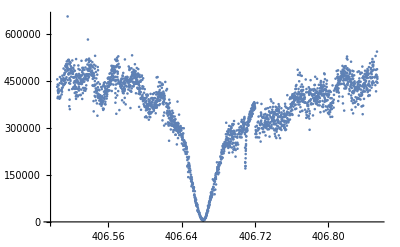

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]],refspec[[2;;,9]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

```mathematica
Plot[(8971*Abs[r[x,406.66,.006,.033,0.0001,-.05,-7,0]]^2),{x,406.5,406.9},PlotRange->All]
```

-Graphics-

```mathematica
711-665
```

46

```mathematica
xyreal//Length
```

2398

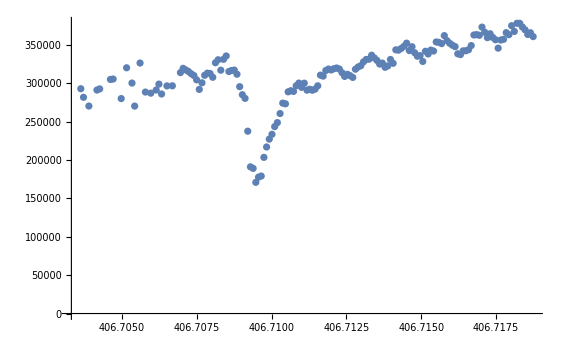

```mathematica
ListPlot[xyreal[[1350;;1500]]]
```

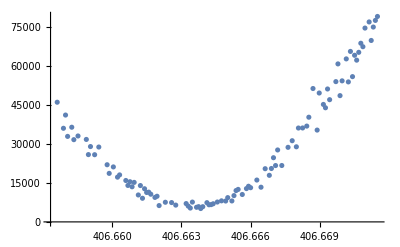

```mathematica
ListPlot[xyreal[[1050;;1150]]]
```

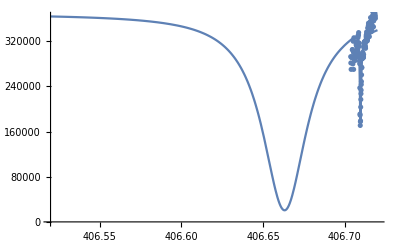

```mathematica
Show[
Plot[368438.936673*(Abs[r[ω,406.7092165,406.6635,0.00385527,0.020403122,0.033,0.0007915748871]])^2,{ω,406.52,406.72}],
ListPlot[xyreal[[1350;;1500]]]
]
```

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-1841.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2581.75] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
ωa | 406.709 | 0.000096597 | 4.21037×10^6 | 0.
ωc | 406.663 | 5.64737×10^-7 | 7.20092×10^8 | 0.
g | 0.00385527 | 0.000350058 | 11.0132 | 7.63004×10^-21
κ1 | 0.0204031 | 0.00347428 | 5.87263 | 2.842×10^-8
κ2 | 0.04 | 0. | ∞ | 0.
γ | 0.000791575 | 0.0000939283 | 8.42744 | 3.312×10^-14
amp | 368439. | 4669.89 | 78.8967 | 2.17475×10^-120

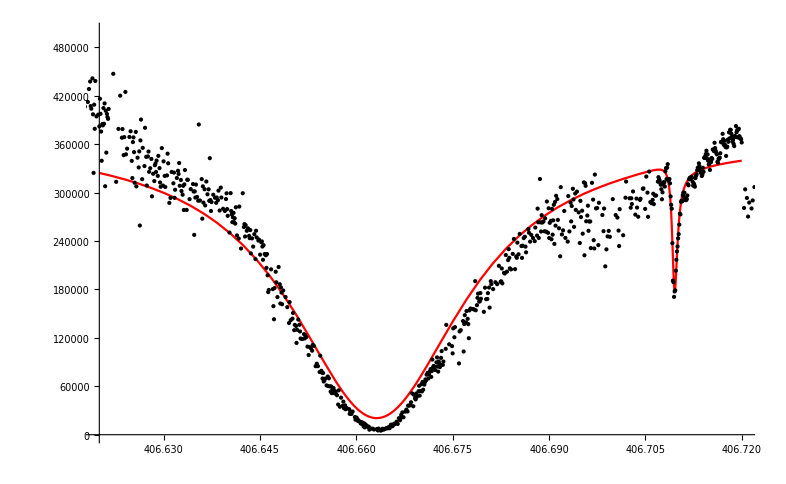

```mathematica
Cfit=NonlinearModelFit[xyreal[[1350;;1500]],amp*(Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]])^2/.{ωc-> 406.6635,κ2-> 0.033},{{ωa,406.709},{ωc,406.663},{g,.003},{κ1,0.01},{κ2,0.04},{γ,0.0001},{amp,450000}},ω];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,406.62,406.72},Epilog->Point[xyreal],PlotStyle->Red,PlotRange->{0,500000}]
```

```mathematica
xyreal
```

{{406.504,431795.},{406.504,455686.},{406.505,395525.},{406.505,438976.},{406.505,420477.},{406.505,399752.},{406.505,416915.},{406.505,414522.},{406.506,411828.},{406.506,421727.},2379,{406.852,448571.},{406.852,469809.},{406.853,447105.},{406.853,544216.},{406.853,487938.},{406.853,461762.},{406.853,464419.},{406.853,457344.},{406.853,444489.}}
 |  |  |  |

```mathematica
Partition[xyreal,binby]
```

{{{406.504,431795.},{406.504,455686.}},{{406.505,395525.},{406.505,438976.}},{{406.505,420477.},{406.505,399752.}},{{406.505,416915.},{406.505,414522.}},1191,{{406.852,469809.},{406.853,447105.}},{{406.853,544216.},{406.853,487938.}},{{406.853,461762.},{406.853,464419.}},{{406.853,457344.},{406.853,444489.}}}
 |  |  |  |

```mathematica
Dimensions[xybin]
```

{1199,2}

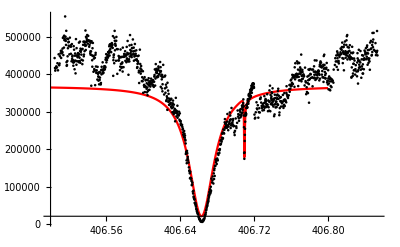

```mathematica
binby=2;
xybin=Total[Partition[xyreal,binby]ᵀ/binby];
Show[{Plot[Cfit[x],{x,406.5,406.8},PlotStyle->Red,PlotRange-> All],ListPlot[xybin,PlotStyle->Black]}]
```

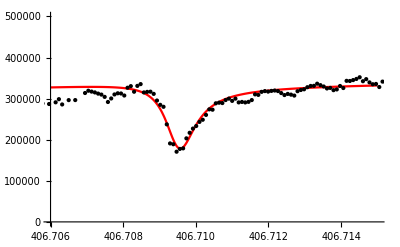

```mathematica
Plot[Cfit[x],{x,406.706,406.715},Epilog->Point[xyreal],PlotStyle->Red,PlotRange->{0,500000}]
```

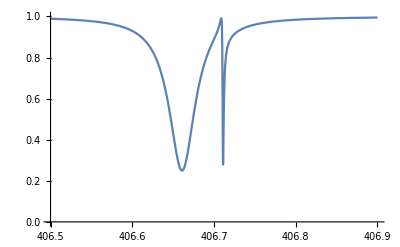

```mathematica
Plot[Abs[r[ω,406.709,406.663,0.01,0.01,0.04,0.0001]]^2,{ω,406.5,406.9}, PlotRange->{0,1}]
```

#### Bare cavity:

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

```mathematica
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*reflection1.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

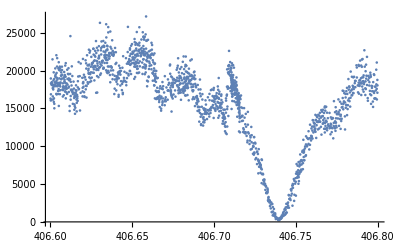

```mathematica
refspec=Import[names[[1]],"Table"];
xydata=Total[Partition[{refspec[[2;;,1]],refspec[[2;;,5]]}ᵀ,1]ᵀ/1];trimxy=xydata/."NaN"-> Sequence[];mask=Length[#]>1&/@trimxy;xyreal=Complement[trimxy*Boole[mask],{{0}}][[2;;]];
ListPlot[xyreal]
```

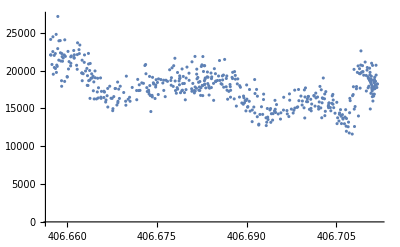

```mathematica
ListPlot[xyreal[[500;;1000]]]
```

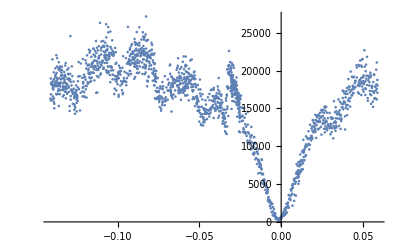

```mathematica
Cnorm={xyreal[[All,1]]-406.741,xyreal[[All,2]]}ᵀ;
ListPlot[Cnorm]
```

| Estimate | Standard Error | t-Statistic | P-Value
ωc | 0.0000850776 | 0.000193234 | 0.440282 | 0.659792
κ1 | 0.0139009 | 0.000481628 | 28.8624 | 9.83536×10^-148
κ2 | 0.0330766 | 0.000674621 | 49.03 | 1.15269571203×10^-320
α | 0.1 | 0. | ∞ | 0.
ϕ | 0. | 0. | ComplexInfinity | 0.
amp | 20060.1 | 85.5289 | 234.542 | 1.28305943459×10^-1238

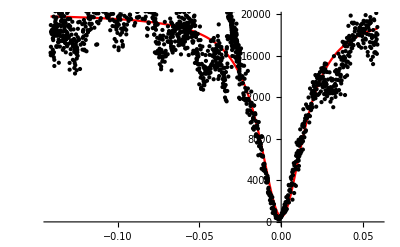

```mathematica
Cfit=NonlinearModelFit[Cnorm,amp*Abs[r[ω, ωa, ωc, g, κ1,κ2, γ]]^2/.{g-> 0,γ-> 0.0001,ωa-> 0},{{ωc,-0.01},{κ1,0.01},{κ2, 0.04},{α,0.1},{ϕ,0},{amp,20000}},ω];
Cfit["ParameterTable"]
Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},Epilog->Point[Cfit["Data"]],PlotStyle->Red]
```

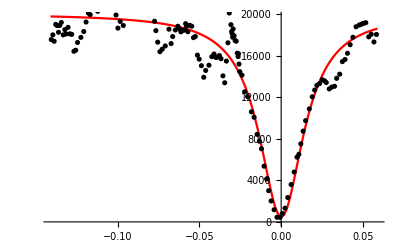

```mathematica
binby=10;
xybin=Total[Partition[Cnorm,binby]ᵀ/binby];
Show[{Plot[Cfit[x],{x,Cfit["Data"][[1,1]],Cfit["Data"][[-1,1]]},PlotStyle->Red],ListPlot[xybin,PlotStyle->Black]}]
```

```mathematica
fitκ1 = κ1/.Cfit["BestFitParameters"];
fitκ2 = κ2/.Cfit["BestFitParameters"];
fitCamp = amp/.Cfit["BestFitParameters"];
```

#### SiV on resonance

```mathematica
SetDirectory[NotebookDirectory[]];
names=
Sort[Cases[FileNames[],_?((StringMatchQ[#,"*PLE*image.txt"])&&!StringMatchQ[#,"*History*"]&)],FileDate[#1,"Modification"]<FileDate[#2,"Modification"]&];
Table[Print[i,": ",names[[i]]],{i,1,Length[names]}];
```

1: 14.45.08_Pulse Experiment_Two laser PLE_ID8_image.txt

2: 13.20.05_Pulse Experiment_SiV PLE  on resonance_ID1_image.txt

3: 10.50.18_Pulse Experiment_1laser PLE  1Mcts , NO green_ID5_image.txt

4: 15.27.58_Pulse Experiment_PLE SiV dn_ID7_image.txt

5: 15.29.50_Pulse Experiment_PLE SiV up_ID8_image.txt

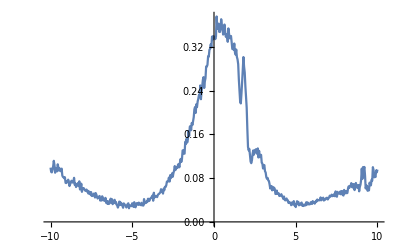

```mathematica
data=Import[#,"Table"]&/@names;
XYdata=Total[Partition[{data[[2,All,1]],data[[2,All,2]]}ᵀ,1]ᵀ/1];
ListLinePlot[XYdata]
```

```mathematica
Rnorm={XYdata[[All,1]]/1000,XYdata[[All,2]]}ᵀ;
```

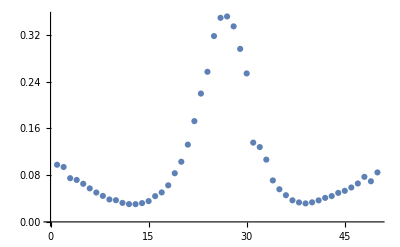

```mathematica
ListPlot[Total[Partition[XYdata[[All,2]],10]ᵀ/10]]
```

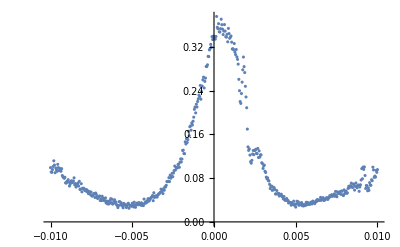

```mathematica
ListPlot[Rnorm]
```

```mathematica
r[ω_, ωa_, ωc_, g_, κ1_,κ2_, γ_] := 1-κ1/(ⅈ(ω-ωc)+κ2/2+g^2/(ⅈ(ω-ωa)+γ/2));
```

| Estimate | Standard Error | t-Statistic | P-Value
ωa | 0.000472911 | 0.0000118237 | 39.9971 | 4.94731×10^-157
ωc | -0.0000924584 | 0.0000707438 | -1.30695 | 0.191839
κ1 | 0.0116329 | 0.0000519692 | 223.842 | 9.63968069911×10^-499
g | 0.00524702 | 0.0000210022 | 249.832 | 4.20018565015×10^-522
α | 0.1 | 0. | ∞ | 0.
ϕ | 0. | 0. | ComplexInfinity | 0.
amp | 0.379425 | 0.00204255 | 185.76 | 3.31799614479×10^-459

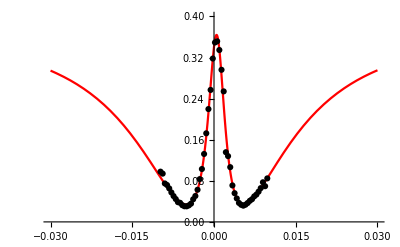

```mathematica
Rfit=NonlinearModelFit[Rnorm,amp*Abs[r[ω, ωa, ωc, g, κ1,κ2, γ]]^2/.{κ2-> fitκ2,γ-> 0.0001},{{ωa,0},{ωc,0},{κ1,fitκ1},{g,0.006},{α,0.1},{ϕ,0},{amp,1}},ω];
Rfit["ParameterTable"]
binby=10;
Rxybin=Total[Partition[Rnorm,binby]ᵀ/binby];
Show[{Plot[Rfit[x],{x,-.03,.03},PlotStyle->Red,PlotRange->{0,0.4}],ListPlot[Rxybin,PlotStyle->Black]}]
```

```mathematica
fitg = g/.Rfit["BestFitParameters"];
fitRamp = amp/.Rfit["BestFitParameters"];
```

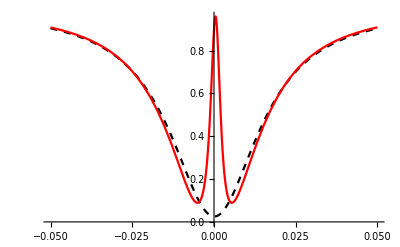

```mathematica
Plot[{Cfit[x]/fitCamp,Rfit[x]/fitRamp},{x,-.05,.05},PlotStyle->{Directive[Black,Dashed],Red}]
```

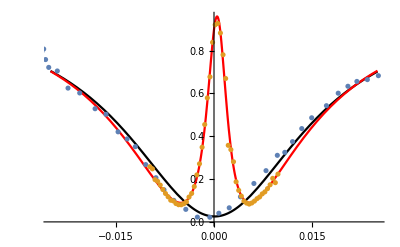

```mathematica
Show[{Plot[{Cfit[x]/fitCamp,Rfit[x]/fitRamp},{x,-.025,.025},PlotStyle->{Black,Red},AxesOrigin-> -.05],ListPlot[{(xybinᵀ*{1,1/fitCamp})ᵀ[[20;;-20]],(Rxybinᵀ*{1,1/fitRamp})ᵀ}]}]
```

```mathematica
(4*fitg^2)/(fitκ2*0.0001)
```

33.2939

```mathematica
Rfit[0]/fitRamp
```

0.898084

#### Cavity half-detuned

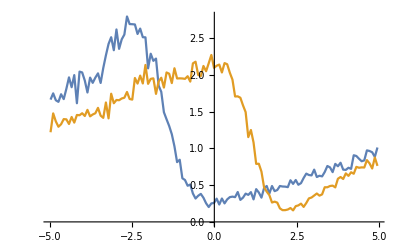

```mathematica
rawdn=Total[Partition[{data[[4,All,1]],data[[4,All,2]]}ᵀ,4]ᵀ/4];
rawup=Total[Partition[{data[[5,All,1]],data[[5,All,2]]}ᵀ,4]ᵀ/4];
XYdatadn={rawdn[[All,1]],rawdn[[All,2]]}ᵀ;
XYdataup={rawup[[All,1]],rawup[[All,2]]}ᵀ;
ListLinePlot[{XYdatadn,XYdataup}]
```

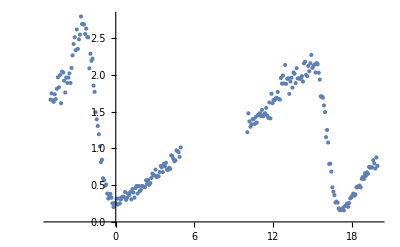

```mathematica
ListPlot[Flatten[{XYdatadn,(XYdataupᵀ+{15,0})ᵀ},1]]
```

```mathematica
JointFit=NonlinearModelFit[Flatten[{XYdatadn,(XYdataupᵀ+{15,0})ᵀ},1],If[ω<7,amp1*Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2,amp2*Abs[r[ω-15,ωa2,ωc,g2,κ1,κ2,γ]]^2]/.{κ2-> fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{g1,fitg*1000},{g2,fitg*1000},{ωa1,-2.5},{ωa2,-0.2},{ωc,-12},{amp1,2.5},{amp2,2}},ω]
JointFit["ParameterTable"]
```

FittedModel[If[ω<7,2.50601 Abs[r[ω,-2.53141,«3»,33.0766,0.1]]^2,2.33305 Abs[r[ω-15,-0.205697,-12.6126,6.15004,12.2252,33.0766,0.1]]^2]]

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 12.2252 | 0.24122 | 50.6807 | 7.36565×10^-131
g1 | 5.82265 | 0.0890929 | 65.3549 | 9.32807×10^-156
g2 | 6.15004 | 0.0807597 | 76.1523 | 4.40964×10^-171
ωa1 | -2.53141 | 0.0330108 | -76.6841 | 8.74924×10^-172
ωa2 | -0.205697 | 0.0372737 | -5.51856 | 8.77667×10^-8
ωc | -12.6126 | 0.32365 | -38.9698 | 2.86263×10^-106
amp1 | 2.50601 | 0.028525 | 87.853 | 1.40083×10^-185
amp2 | 2.33305 | 0.0262658 | 88.8244 | 1.05997×10^-186

```mathematica
binby = 4;
Dxybin = Total[Partition[XYdatadn,binby]ᵀ/binby];
Uxybin = Total[Partition[XYdataup,binby]ᵀ/binby];
```

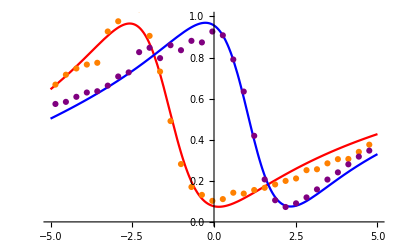

```mathematica
Show[{Plot[{Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]],Abs[r[ω,ωa2,ωc,g2,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]]},{ω,-5,5},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{(Dxybinᵀ*{1,1/amp1/.JointFit["BestFitParameters"]})ᵀ,(Uxybinᵀ*{1,1/amp2/.JointFit["BestFitParameters"]})ᵀ},PlotStyle->{Orange,Purple}]}]
```

#### Few kappa detuned

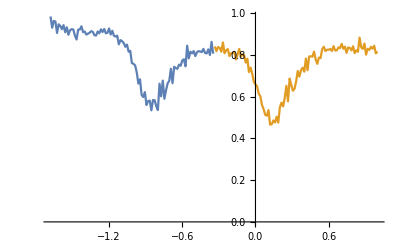

```mathematica
XYdataS=Total[Partition[{data[[3,All,1]],(data[[3,All,2]])/(Max[data[[3,All,2]]])}ᵀ,1]ᵀ/1];
ListLinePlot[{XYdataS[[100;;200]],XYdataS[[201;;]]},AxesOrigin->0]
```

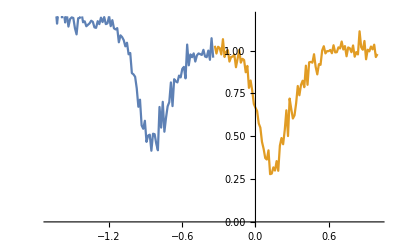

```mathematica
XYdataS=Total[Partition[{data[[3,All,1]],2*(data[[3,All,2]]-Mean[data[[3,All,2]]])/(Max[data[[3,All,2]]])+1}ᵀ,1]ᵀ/1];
ListLinePlot[{XYdataS[[100;;200]],XYdataS[[201;;]]},AxesOrigin->0,PlotRange->{0,1.2}]
```

```mathematica
XYdataSup=XYdataS[[100;;200]];
XYdataSdn=XYdataS[[201;;]];
```

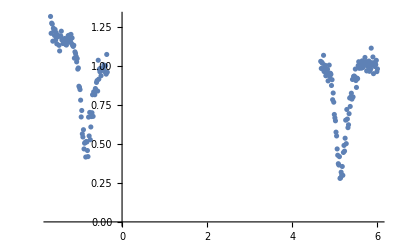

```mathematica
ListPlot[Flatten[{XYdataSup,(XYdataSdnᵀ+{5,0})ᵀ},1]]
```

```mathematica
JointFitS=NonlinearModelFit[Flatten[{XYdataSdn,(XYdataSupᵀ+{5,0})ᵀ},1],If[ω<2,amp1*Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2,amp2*Abs[r[ω-5,ωa2,ωc,g2,κ1,κ2,γ]]^2]/.{g1-> fitg*1000,g2-> fitg*1000,κ1-> fitκ1*1000,κ2-> fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{g1,fitg*1000},{g2,fitg*1000},{ωa1,0.2},{ωa2,0.2},{ωc,60},{amp1,1},{amp2,1}},ω]
JointFitS["ParameterTable"]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[If[ω<2,1.44607 Abs[r[ω,-12.8852,«3»,33.0766,0.1]]^2,3.04604 Abs[r[ω-5,2.79453,17.1397,5.24702,13.9009,33.0766,0.1]]^2]]

General::munfl: (9.42789×10^-22)^97. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.39093×10^-21)^97. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.03786×10^-22)^97. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 13.9009 | 3.06444×10^-11 | 4.53622×10^11 | 0.
g1 | 5.24702 | 1.40496×10^-11 | 3.73463×10^11 | 0.
g2 | 5.24702 | 6.56592×10^-12 | 7.99129×10^11 | 0.
ωa1 | -12.8852 | 740.821 | -0.0173932 | 0.986141
ωa2 | 2.79453 | 3.52708 | 0.792307 | 0.42915
ωc | 17.1397 | 16.3558 | 1.04792 | 0.295977
amp1 | 1.44607 | 8.23459 | 0.175609 | 0.860784
amp2 | 3.04604 | 3.36474 | 0.905281 | 0.36644

```mathematica
binby=5;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
```

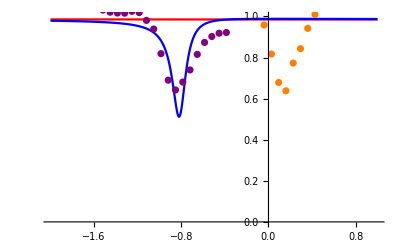

```mathematica
Show[{Plot[{Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFitS["BestFitParameters"]],Abs[r[ω,ωa2,ωc,g2,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFitS["BestFitParameters"]]},{ω,-2,1},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{(SDxybinᵀ*{1,1/amp1/.JointFitS["BestFitParameters"]})ᵀ,(SUxybinᵀ*{1,1/amp2/.JointFitS["BestFitParameters"]})ᵀ},PlotStyle->{Orange,Purple}]}]
```

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 3.44069 | 0.210678 | 16.3315 | 1.01316×10^-29
ωa | 1.2707 | 0.0599027 | 21.2127 | 2.0786×10^-38
ωc | 28.0077 | 2.32686 | 12.0367 | 5.01458×10^-21

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 4.85237 | 0.368227 | 13.1777 | 2.01148×10^-23
ωa | -0.214774 | 0.0276603 | -7.76469 | 8.03194×10^-12
ωc | 52.0013 | 2.67075 | 19.4707 | 1.87023×10^-35

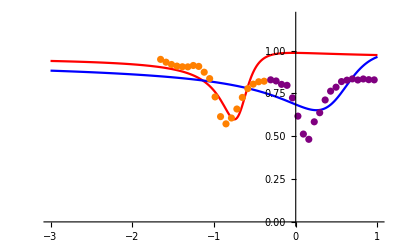

```mathematica
SDfit=NonlinearModelFit[XYdataSdn,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> fitg*1000,κ2->fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{ωa,0.2},{ωc,60}},ω];
SUfit=NonlinearModelFit[XYdataSup,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> fitg*1000,κ2->fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{ωa,0.2},{ωc,60}},ω];
SDfit["ParameterTable"]
SUfit["ParameterTable"]
binby=5;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
Show[{Plot[{SUfit[x],SDfit[x]},{x,-3,1},PlotStyle->{Red,Blue},PlotRange->{0,1.2}],ListPlot[{SUxybin,SDxybin},PlotStyle->{Orange, Purple}]}]
```

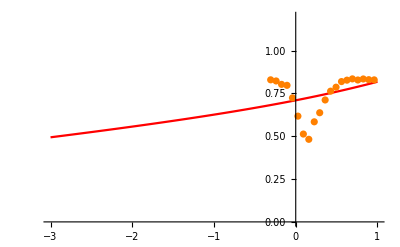

```mathematica
SDfit=NonlinearModelFit[XYdataSdn,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> fitg*1000,κ1->fitκ1*1000,κ2->fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{ωa,0.2},{ωc,20}},ω];
Show[{Plot[SDfit[x],{x,-3,1},PlotStyle->{Red},PlotRange->{0,1.2}],ListPlot[SDxybin,PlotStyle->Orange]}]
```

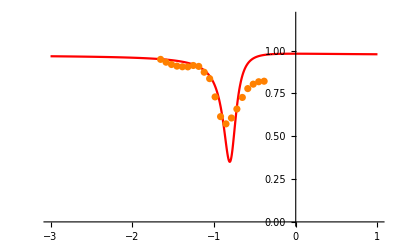

```mathematica
SUfit=NonlinearModelFit[XYdataSup,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> fitg*1000,κ1->fitκ1*1000,κ2->fitκ2*1000,γ-> 0.1},{{κ1,10},{ωa,-0.8},{ωc,60}},ω];
Show[{Plot[SUfit[x],{x,-3,1},PlotStyle->{Red},PlotRange->{0,1.2}],ListPlot[SUxybin,PlotStyle->Orange]}]
```

```mathematica
SDfit["ParameterTable"]
SUfit["ParameterTable"]
```

General::munfl: (2.34372×10^-31)^49. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 13.9009 | 6.79804×10^-16 | 2.04484×10^16 | 0.
ωa | 2.29612 | 0.327738 | 7.00597 | 3.12382×10^-10
ωc | -13.7545 | 2.20542 | -6.23666 | 1.13517×10^-8

General::munfl: (2.24796×10^-32)^49. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 10. | 1.51454×10^-16 | 6.60266×10^16 | 0.
ωa | -0.525353 | 0.0108757 | -48.3053 | 3.77624×10^-70
ωc | 98.2323 | 3.11807 | 31.5042 | 4.48158×10^-53

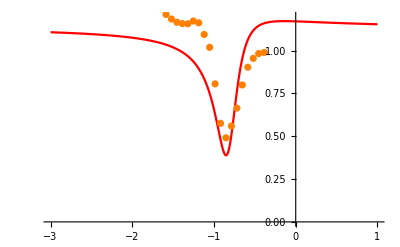

```mathematica
Show[{Plot[1.2*Abs[r[x,-0.4,60,5.2,10,33,0.1]]^2,{x,-3,1},PlotStyle->{Red},PlotRange->{0,1.2}],ListPlot[SUxybin,PlotStyle->Orange]}]
```

### Few kappa detuned, different dataset

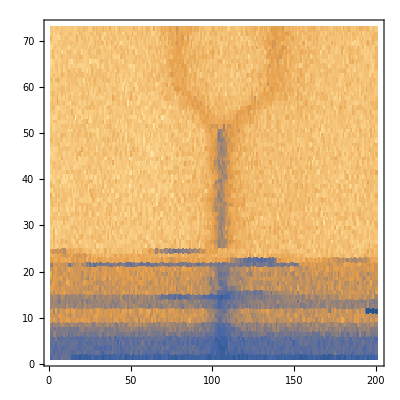

```mathematica
siv1F=Import["C:\\Users\\Newpurt\\Dropbox (Lukin SiV)\\Spin-photon paper (2019)\\SI\\Strain and B\\SiV2 6A y\\10.56.10_Pulse Experiment_SiV in A96L9 ramp to 6A Y (History 1F)_ID2_image.txt","Table"];
xlist=Import["C:\\Users\\Newpurt\\Dropbox (Lukin SiV)\\Spin-photon paper (2019)\\SI\\Strain and B\\SiV2 6A y\\10.56.10_Pulse Experiment_SiV in A96L9 ramp to 6A Y_ID2_image.txt","Table"][[All,1]];
ListDensityPlot[siv1F, InterpolationOrder->0]
```

```mathematica
siv1F=Import["C:\\Users\\ctn20\\Dropbox (Lukin SiV)\\Spin-photon paper (2019)\\SI\\Strain and B\\SiV2 6A y\\10.56.10_Pulse Experiment_SiV in A96L9 ramp to 6A Y (History 1F)_ID2_image.txt","Table"];
xlist=Import["C:\\Users\\ctn20\\Dropbox (Lukin SiV)\\Spin-photon paper (2019)\\SI\\Strain and B\\SiV2 6A y\\10.56.10_Pulse Experiment_SiV in A96L9 ramp to 6A Y_ID2_image.txt","Table"][[All,1]];
ListDensityPlot[siv1F, InterpolationOrder->0]
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

ListDensityPlot::arrayerr: $Failed must be a valid array.

ListDensityPlot[$Failed,InterpolationOrder→0]

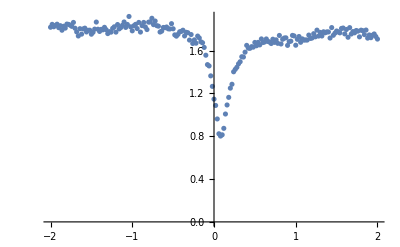

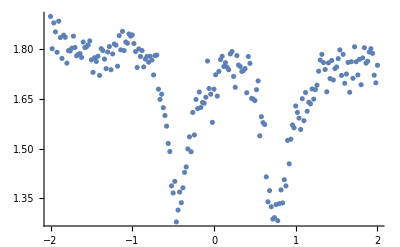

```mathematica
b0=Mean[siv1F[[25;;50]]];
ListPlot[{xlist,b0}ᵀ,PlotRange->All]
b1=Mean[siv1F[[60;;]]];
ListPlot[{xlist,b1}ᵀ,PlotRange->All]
```

```mathematica
((b1-(Mean[b1[[1;;50]]]))*3)/Mean[b1[[1;;50]]]+1
```

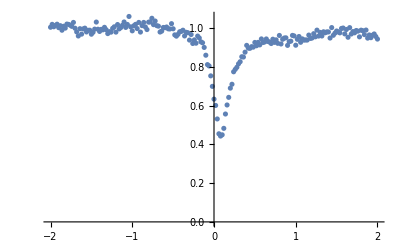

```mathematica
b0list={xlist,((b0-(Mean[b0[[1;;50]]]))*1)/Mean[b0[[1;;50]]]+1}ᵀ;
ListPlot[b0list,PlotRange->All]
```

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 10.5531 | 0.438935 | 24.0424 | 1.22405×10^-60
ωa | -0.235953 | 0.00759104 | -31.083 | 4.24477×10^-78
ωc | -89.4116 | 1.97869 | -45.1873 | 2.95346×10^-106

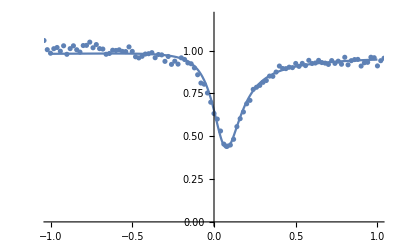

```mathematica
b0fit=NonlinearModelFit[b0list,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{g-> fitg*1000,κ2->fitκ2*1000,γ-> 0.1},{{κ1,fitκ1*1000},{ωa,0.2},{ωc,-60}},ω];
b0fit["ParameterTable"]
binby=1;
b0bin=Total[Partition[b0list,binby]ᵀ/binby];
Show[{Plot[b0fit[x],{x,-1,1},PlotRange->{0,1.2}],ListPlot[b0bin]}]
```

```mathematica
ωcfit=ωc/.b0fit["BestFitParameters"]
κ1fit=κ1/.b0fit["BestFitParameters"]
```

123.059

18.3172

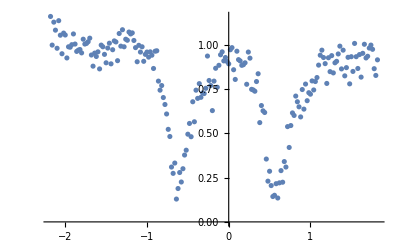

```mathematica
b1list={xlist-0.18,((b1-(Mean[b1[[1;;50]]]))*3)/Mean[b1[[1;;50]]]+1}ᵀ;
(*b1list={xlist-0.18,b1/Mean[b1[[1;;50]]]}ᵀ;*)
ListPlot[b1list,PlotRange->All]
```

```mathematica
b1list[[1]]
```

{-2.,1.1063}

```mathematica
b1list[[115]]
```

{0.,0.975545}

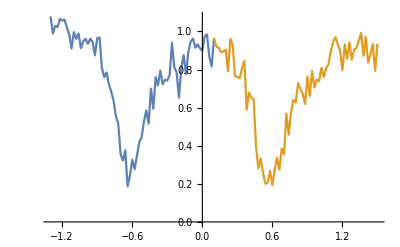

```mathematica
ListLinePlot[{b1list[[45;;115]],b1list[[115;;185]]},AxesOrigin->0]
```

```mathematica
XYdataSup=b1list[[45;;115]];
XYdataSdn=b1list[[115;;185]];
```

```mathematica
g1->  fitg*1000
,g2-> fitg*1000,
```

```mathematica
JointFitS=NonlinearModelFit[Flatten[{XYdataSdn,(XYdataSupᵀ+{5,0})ᵀ},1],If[ω<2,Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2,Abs[r[ω-5,ωa2,ωc,g2,κ1,κ2,γ]]^2]/.{κ2-> fitκ2*1000,γ-> 0.1},{{κ1,κ1fit},{g1,fitg*1000},{g2,fitg*1000},{ωa1,0.97},{ωa2,-0.37},{ωc,90}},ω]
JointFitS["ParameterTable"]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[If[ω<2,Abs[«1»]^2,Abs[r[ω-5,37.5007,15665.8,774.941,13.4441,33.0766,0.1]]^2]]

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 13.4441 | 3.68366 | 3.64967 | 0.000336703
g1 | 1035.33 | 5451.02 | 0.189933 | 0.849558
g2 | 774.941 | 4072.99 | 0.190263 | 0.8493
ωa1 | 68.5711 | 352.094 | 0.194752 | 0.845789
ωa2 | 37.5007 | 196.572 | 0.190774 | 0.8489
ωc | 15665.8 | 84359.5 | 0.185703 | 0.852869

```mathematica
binby=2;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
```

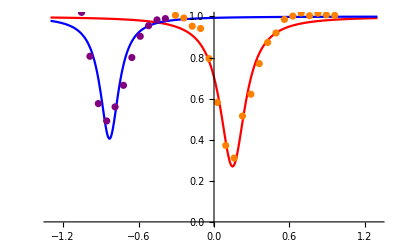

```mathematica
Show[{Plot[{Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFitS["BestFitParameters"]],Abs[r[ω,ωa2,ωc,g2,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFitS["BestFitParameters"]]},{ω,-1.3,1.3},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{SDxybin,SUxybin},PlotStyle->{Orange,Purple}]}]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
g | 669.877 | 4747.82 | 0.141091 | 0.88809
κ1 | 13.468 | 2.25977 | 5.95989 | 4.07198×10^-8
ωa | 44.3904 | 310.324 | 0.143046 | 0.886551
ωc | 10142.7 | 72633.5 | 0.139642 | 0.889232

| Estimate | Standard Error | t-Statistic | P-Value
g | 913.253 | 12514. | 0.0729783 | 0.941974
κ1 | 13.4109 | 9.93257 | 1.3502 | 0.180095
ωa | 44.3804 | 603.993 | 0.0734784 | 0.941577
ωc | 18446.4 | 259153. | 0.0711797 | 0.943401

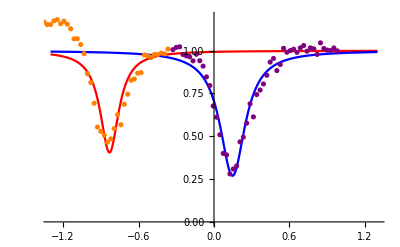

```mathematica
SDfit=NonlinearModelFit[XYdataSdn,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{κ2->fitκ2*1000,γ-> 0.1},{{g,fitg*1000},{κ1,fitκ1*1000},{ωa,0.5},{ωc,ωcfit}},ω];
SUfit=NonlinearModelFit[XYdataSup,Abs[r[ω,ωa,ωc,g,κ1,κ2,γ]]^2/.{κ2->fitκ2*1000,γ-> 0.1},{{g,fitg*1000},{κ1,fitκ1*1000},{ωa,-0.7},{ωc,ωcfit}},ω];
SDfit["ParameterTable"]
SUfit["ParameterTable"]
binby=2;
SDxybin=Total[Partition[XYdataSdn,binby]ᵀ/binby];
SUxybin=Total[Partition[XYdataSup,binby]ᵀ/binby];
Show[{Plot[{SUfit[x],SDfit[x]},{x,-1.3,1.3},PlotStyle->{Red,Blue},PlotRange->{0,1.2}],ListPlot[{SUxybin,SDxybin},PlotStyle->{Orange, Purple}]}]
```

## All Cavity detunings together!

```mathematica
Show[{Plot[{SUfit[x],SDfit[x]},{x,-1.3,1.3},PlotStyle->{Red,Blue},PlotRange->{0,1.2}],ListPlot[{SUxybin,SDxybin},PlotStyle->{Orange, Purple}]}]
```

-Graphics-

```mathematica
SUfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
g | 913.253 | 12514. | 0.0729783 | 0.941974
κ1 | 13.4109 | 9.93257 | 1.3502 | 0.180095
ωa | 44.3804 | 603.993 | 0.0734784 | 0.941577
ωc | 18446.4 | 259153. | 0.0711797 | 0.943401

```mathematica
Show[{Plot[b0fit[x],{x,-1,1},PlotRange->{0,1.2}],ListPlot[b0bin]}]
```

-Graphics-

```mathematica
b0fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 10.5531 | 0.438935 | 24.0424 | 1.22405×10^-60
ωa | -0.235953 | 0.00759104 | -31.083 | 4.24477×10^-78
ωc | -89.4116 | 1.97869 | -45.1873 | 2.95346×10^-106

```mathematica
Show[{Plot[{Abs[r[ω,ωa1,ωc,g1,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]],Abs[r[ω,ωa2,ωc,g2,κ1,κ2,γ]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]]},{ω,-5,5},PlotStyle->{Red,Blue},PlotRange->{0,1}],ListPlot[{(Dxybinᵀ*{1,1/amp1/.JointFit["BestFitParameters"]})ᵀ,(Uxybinᵀ*{1,1/amp2/.JointFit["BestFitParameters"]})ᵀ},PlotStyle->{Orange,Purple}]}]
```

-Graphics-

```mathematica
JointFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
κ1 | 12.2252 | 0.24122 | 50.6807 | 7.36567×10^-131
g1 | 5.82265 | 0.0890929 | 65.3549 | 9.32805×10^-156
g2 | 6.15004 | 0.0807597 | 76.1523 | 4.40964×10^-171
ωa1 | -2.53141 | 0.0330108 | -76.6841 | 8.74922×10^-172
ωa2 | -0.205697 | 0.0372737 | -5.51856 | 8.77667×10^-8
ωc | -12.6126 | 0.32365 | -38.9698 | 2.86263×10^-106
amp1 | 2.50601 | 0.028525 | 87.853 | 1.40082×10^-185
amp2 | 2.33305 | 0.0262658 | 88.8244 | 1.05997×10^-186

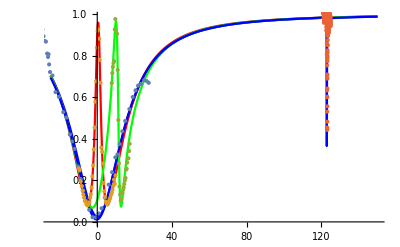

```mathematica
Show[{Plot[{Cfit[x/1000]/fitCamp,Rfit[x/1000]/fitRamp,Abs[r[(x+ωc)/1000,ωa1/1000,ωc/1000,g1/1000,κ1/1000,κ2/1000,γ/1000]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]],b0fit[-(x+89.4)]},{x,-25,150},PlotStyle->{Blue,Red,Green},AxesOrigin-> -.05],ListPlot[{(xybinᵀ*{1000,1/fitCamp})ᵀ[[20;;-20]],(Rxybinᵀ*{1000,1/fitRamp})ᵀ,(Dxybinᵀ*{1,1/amp1/.JointFit["BestFitParameters"]}+{12.613,0})ᵀ,(b0binᵀ+{-89.4,0})ᵀ}]}]
```

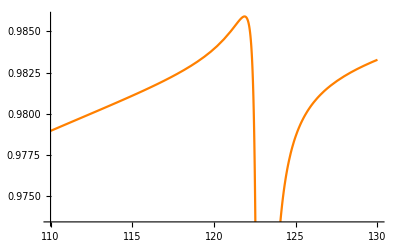

```mathematica
Plot[b0fit[-(x-123)],{x,110,130},PlotStyle->Orange]
```

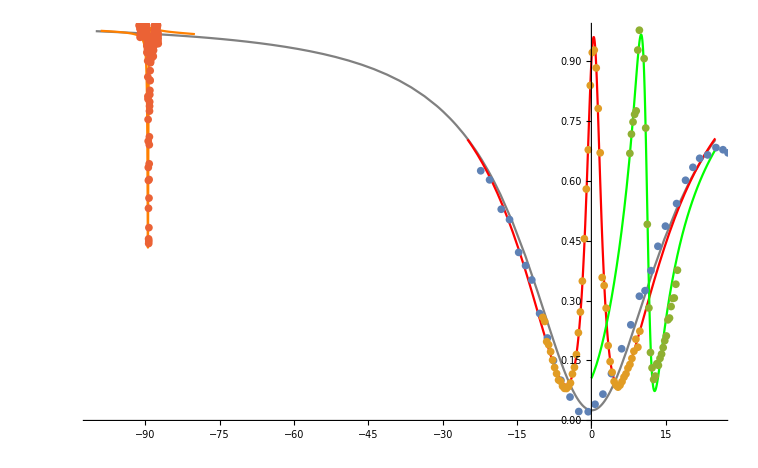

```mathematica
Show[{Plot[Cfit[x/1000]/fitCamp,{x,-100,25},PlotStyle->Gray],Plot[Rfit[x/1000]/fitRamp,{x,-25,25},PlotStyle->Red],Plot[Abs[r[(x+ωc)/1000,ωa1/1000,ωc/1000,g1/1000,κ1/1000,κ2/1000,γ/1000]]^2/.Join[{κ2-> fitκ2*1000,γ-> 0.1},JointFit["BestFitParameters"]],{x,0,25},PlotStyle->Green],Plot[b0fit[-(x+89.4)],{x,1-100,-80},PlotStyle->Orange,PlotRange->All],ListPlot[{(xybinᵀ*{1000,1/fitCamp})ᵀ[[110;;-20]],(Rxybinᵀ*{1000,1/fitRamp})ᵀ,(Dxybinᵀ*{1,1/amp1/.JointFit["BestFitParameters"]}+{12.613,0})ᵀ,(b0binᵀ+{-89.4,0})ᵀ}]}]
```